```mathematica
R=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\eaaa.dat","Table"];
```

```mathematica
R=Differences[Log[R]];
```

```mathematica
ListPointPlot3D[R]
```

-Graphics3D-

```mathematica
RandFit={Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\aaa\\eRand1.dat","Table"],1],Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\aaa\\eRand2.dat","Table"],1],Drop[Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\aaa\\eRand3.dat","Table"],1]};
```

```mathematica
S=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\aaa\sim.dat","Table"];
```

```mathematica
ListPointPlot3D[S,PlotRange->All]
```

-Graphics3D-

```mathematica
RandS=Table[Sort[Transpose[S][[i]]],{i,3}];RandS=Table[Table[{(i-1)/(Length[RandS[[1]]]-1),RandS[[j,i]]},{i,1,Length[RandS[[1]]]}],{j,3}];
```

```mathematica
RandR=Table[Sort[Transpose[R][[i]]],{i,3}];RandR=Table[Table[{(i-1)/(Length[RandR[[1]]]-1),RandR[[j,i]]},{i,1,Length[RandR[[1]]]}],{j,3}];
```

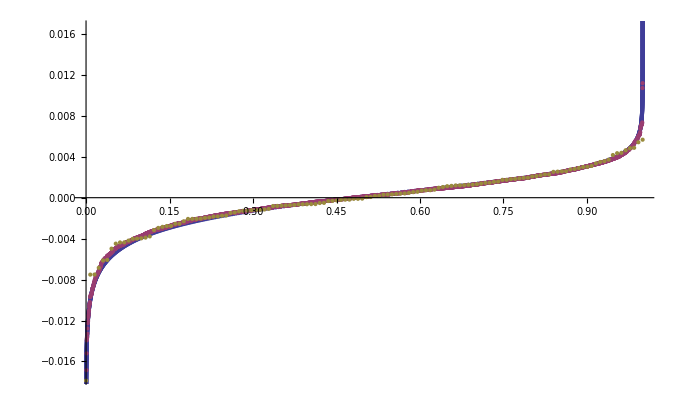

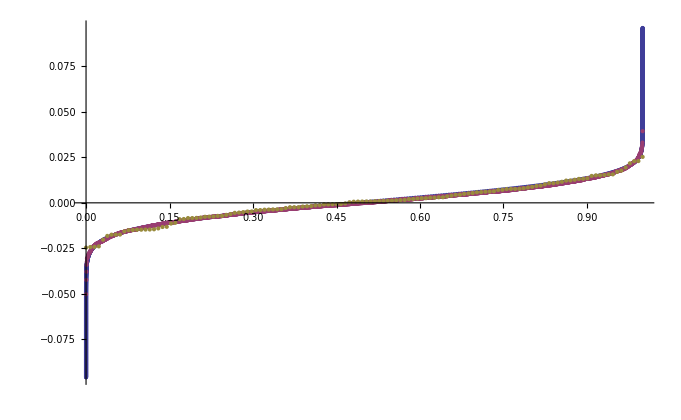

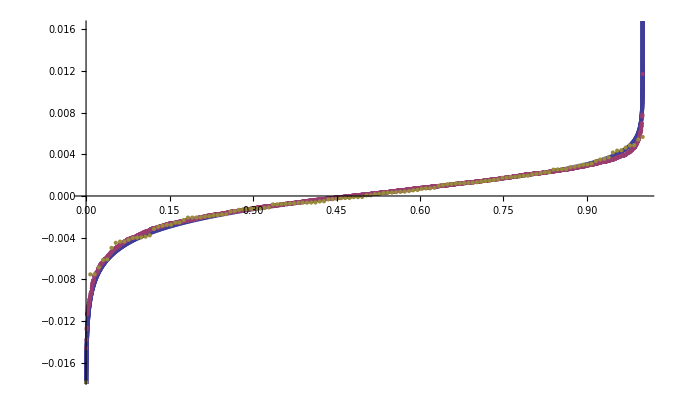

```mathematica
For[i=1,i<=3,i++,Print[ListPlot[{RandFit[[i]],RandS[[i]],RandR[[i]]},Joined->False]]
]
```

```mathematica
Table[Mean[Transpose[S][[i]]],{i,3}]
```

{-0.000175393,-0.000176349,-0.000168065}

```mathematica
Table[Mean[Transpose[RandR[[i]]][[2]]],{i,3}]
```

{-0.000212573,0.000102284,-0.000212573}

```mathematica
S=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\aaa\\simCopula.dat","Table"];
```

```mathematica
RandS=Table[Sort[Transpose[S][[i]]],{i,3}];RandS=Table[Table[{(i-1)/(Length[RandS[[1]]]-1),RandS[[j,i]]},{i,1,Length[RandS[[1]]]}],{j,3}];
```

```mathematica
ListPointPlot3D[S]
```

-Graphics3D-

```mathematica
RandS12={#[[1]],#[[2]]}&/@S;
RandR12={#[[1]],#[[2]]}&/@R;
```

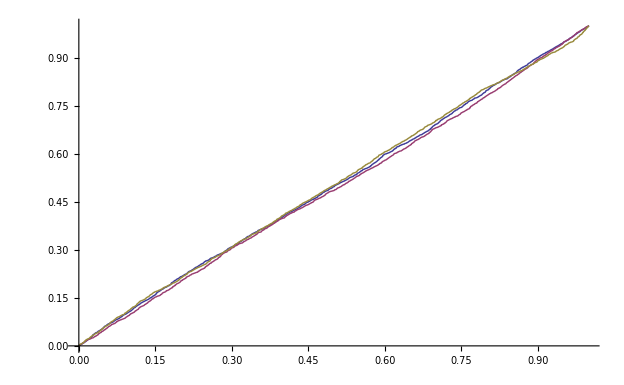

$Aborted

```mathematica
ListPlot[RandS,Joined->True ]
```

```mathematica
RandS[[1,1;;10]]//N
```

{{0.,0.0008},{0.00050025,0.001129},{0.0010005,0.001869},{0.00150075,0.002039},{0.002001,0.002087},{0.00250125,0.00215},{0.0030015,0.002193},{0.00350175,0.002264},{0.004002,0.002558},{0.00450225,0.002725}}

```mathematica
wN=Length[RandS12];F={};For[i=1,i≤wN,i++,
AppendTo[F,{RandS12[[i,1]],RandS12[[i,2]],Length[Select[RandS12,#[[1]]<=RandS12[[i,1]]  && #[[2]]<=RandS12[[i,2]]&]]/wN}];
];
```

```mathematica
wN=Length[RandR12];FR={};For[i=1,i≤wN,i++,
AppendTo[FR,{RandR12[[i,1]],RandR12[[i,2]],Length[Select[RandR12,#[[1]]<=RandR12[[i,1]]  && #[[2]]<=RandR12[[i,2]]&]]/wN}];
]
```

```mathematica
Co=Table[{Select[RandR[[1]],#[[2]]==FR[[i,1]]&][[1,1]],Select[RandR[[2]],#[[2]]==FR[[i,2]]&][[1,1]],FR[[i,3]]},{i,wN}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
Show[ListPointPlot3D[Co,PlotStyle->PointSize[Large]],ListPlot3D[F]]
```

-Graphics3D-

```mathematica
RandS12={#[[2]],#[[3]]}&/@S;
RandR12={#[[2]],#[[3]]}&/@R;
```

```mathematica
wN=Length[RandS12];F={};For[i=1,i≤wN,i++,
AppendTo[F,{RandS12[[i,1]],RandS12[[i,2]],Length[Select[RandS12,#[[1]]<=RandS12[[i,1]]  && #[[2]]<=RandS12[[i,2]]&]]/wN}];
];AppendTo[F,{1,0,0}];AppendTo[F,{0,1,0}];AppendTo[F,{0,0,0}];AppendTo[F,{1,1,1}];
```

```mathematica
wN=Length[RandR12];FR={};For[i=1,i≤wN,i++,
AppendTo[FR,{RandR12[[i,1]],RandR12[[i,2]],Length[Select[RandR12,#[[1]]<=RandR12[[i,1]]  && #[[2]]<=RandR12[[i,2]]&]]/wN}];
]
```

```mathematica
Co=Table[{Select[RandR[[2]],#[[2]]==FR[[i,1]]&][[1,1]],Select[RandR[[3]],#[[2]]==FR[[i,2]]&][[1,1]],FR[[i,3]]},{i,wN}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
Show[ListPointPlot3D[Co,PlotStyle->PointSize[Large]],ListPlot3D[F]]
```

-Graphics3D-